# Développement sur C*[a,b]

## Définition du produit scalaire

### Fonction poid

```mathematica
w:=1
```

### Intervalle d’orthogonalité

```mathematica
a:=-1
```

```mathematica
b:=1
```

### Produit scalaire

```mathematica
⟨f_|g_⟩:=∫_a^b w f* gⅆx
```

## Norme et normalization

### Norme

```mathematica
norm[x_]:=√⟨x|x⟩
```

### Normalization

```mathematica
normalize[x_]:=x/(√⟨x|x⟩)
```

### Normalization d’un ensemble

```mathematica
normalizeListe[vectors_]:=Table[normalize[vectors[[i]]],{i,1,Length[vectors]}]
```

## Projection orthogonale

```mathematica
projection[y_,x_]:=⟨x|y⟩x/⟨x|x⟩
```

## Orthogonalisation (Procédé de Gram-Schmidt)

```mathematica
gramSchmidt[vectors_]:=Module[{oVectors=vectors},
Do[oVectors[[i]]-=projection[oVectors[[i]],oVectors[[j]]],{i,2,Length[vectors]},{j,1,i-1}];
oVectors]
```

### Matrice d’orthonormalité

```mathematica
orthogonality[vectors_]:=Table[⟨vectors[[i]]|vectors[[j]]⟩,{i,1,Length[vectors]},{j,1,Length[vectors]}]//Simplify//TableForm
```

## Base

### Base quelconque

La dimension de la base

```mathematica
dim:=7
```

```mathematica
baseQuelconque=Table[ⅇ^(ⅈ π n x),{n,0,dim-1}]
```

{1,ⅇ^(ⅈ π x),ⅇ^(2 ⅈ π x),ⅇ^(3 ⅈ π x),ⅇ^(4 ⅈ π x),ⅇ^(5 ⅈ π x),ⅇ^(6 ⅈ π x)}

```mathematica
(*baseQuelconque=Table[Sin[n π x] ,{n,1,dim}]*)
```

```mathematica
orthogonality[baseQuelconque]
```

2 | 0 | 0 | 0 | 0 | 0 | 0
0 | 2 | 0 | 0 | 0 | 0 | 0
0 | 0 | 2 | 0 | 0 | 0 | 0
0 | 0 | 0 | 2 | 0 | 0 | 0
0 | 0 | 0 | 0 | 2 | 0 | 0
0 | 0 | 0 | 0 | 0 | 2 | 0
0 | 0 | 0 | 0 | 0 | 0 | 2

### Base orthogonale

```mathematica
Subscript[𝓊, n_][x_]:=gramSchmidt[baseQuelconque][[n]]
```

```mathematica
Table[Subscript[𝓊, n][x],{n,1,dim}]
```

{1,ⅇ^(ⅈ π x),ⅇ^(2 ⅈ π x),ⅇ^(3 ⅈ π x),ⅇ^(4 ⅈ π x),ⅇ^(5 ⅈ π x),ⅇ^(6 ⅈ π x)}

```mathematica
orthogonality[Table[Subscript[𝓊, n][x],{n,1,dim}]]
```

2 | 0 | 0 | 0 | 0 | 0 | 0
0 | 2 | 0 | 0 | 0 | 0 | 0
0 | 0 | 2 | 0 | 0 | 0 | 0
0 | 0 | 0 | 2 | 0 | 0 | 0
0 | 0 | 0 | 0 | 2 | 0 | 0
0 | 0 | 0 | 0 | 0 | 2 | 0
0 | 0 | 0 | 0 | 0 | 0 | 2

### Base orthonormale

```mathematica
Subscript[𝓊̃, n_][x_]:=normalize[Subscript[𝓊, n][x]]//Simplify
```

```mathematica
normalizeListe[Table[Subscript[𝓊, n][x],{n,1,dim}]]//Simplify
```

{1/(√2),ⅇ^(ⅈ π x)/(√2),ⅇ^(2 ⅈ π x)/(√2),ⅇ^(3 ⅈ π x)/(√2),ⅇ^(4 ⅈ π x)/(√2),ⅇ^(5 ⅈ π x)/(√2),ⅇ^(6 ⅈ π x)/(√2)}

```mathematica
orthogonality[Table[Subscript[𝓊̃, n][x],{n,1,dim}]]
```

1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1

## Développement

### La fonction à développer

```mathematica
f[x_] :=π ⅇ^(ⅈ π/2x)
```

### Les coéfficients

```mathematica
Subscript[a, n_]:=⟨Subscript[𝓊̃, n][x]|f[x] ⟩
```

```mathematica
Table[Subscript[a, n],{n,1,dim}]//Simplify
```

{2 √2,2 √2,-(2 √2)/3,(2 √2)/5,-(2 √2)/7,(2 √2)/9,-(2 √2)/11}

### Développement

```mathematica
∑_(n=1)^dim Subscript[a, n] Subscript[𝓊̃, n]//Simplify
```

(2 √2 (3465 (𝓊̃)_1+3465 (𝓊̃)_2-1155 (𝓊̃)_3+693 (𝓊̃)_4-495 (𝓊̃)_5+385 (𝓊̃)_6-315 (𝓊̃)_7))/3465

```mathematica
Fdev[x_]=∑_(n=1)^dim Subscript[a, n] Subscript[𝓊̃, n][x]
```

2+2 ⅇ^(ⅈ π x)-2/3 ⅇ^(2 ⅈ π x)+2/5 ⅇ^(3 ⅈ π x)-2/7 ⅇ^(4 ⅈ π x)+2/9 ⅇ^(5 ⅈ π x)-2/11 ⅇ^(6 ⅈ π x)

## Représentation

### Représentation

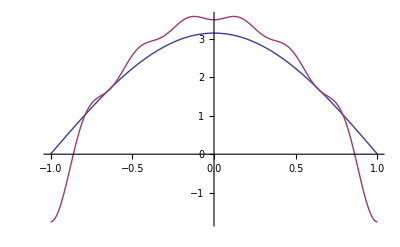

```mathematica
Plot[Evaluate[Re[{f[x],Fdev[x]}]],{x,a,b},PlotRange->All]
```

### Manipulation

```mathematica
Manipulate[Plot[Evaluate[Re[{f[x],∑_(n=1)^N Subscript[a, n] Subscript[𝓊̃, n][x]}]],{x,a,b},PlotRange->All],{N,1,dim,1},ControlType->Setter]
```